## Styling

```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/talks/Séminaire CALIN/img/

```mathematica
(* Thickness *)
th=0.003;
```

```mathematica
(*Styling of the text*)
st=Directive[FontSize->15,FontFamily->"CMU Serif"];
stylize[text_]:=Style[text,st];
```

```mathematica
BostonBlue=RGBColor["#00688B"];
comp=RGBColor["#8B2300"];
```

```mathematica
SetOptions[ListPlot,Frame->True,FrameStyle->st,PlotRange->All,PlotStyle->Black];
```

## Utility functions

```mathematica
(* string substitution *)
Sub[rule_,init_String,l_Integer]:=Nest[StringReplace[#,rule]&,init,l]
```

```mathematica
(* Height (integrated arrow field), can also be seen as the mode k=0 of the Fourier transform of the sequence of arrows *)
Heights[arrows_]:=Table[Total[arrows[[;;N]]],{N,1,Length[arrows]}];
```

```mathematica
(* maximum of the height distribution *)
MaxHeights[heights_]:=Block[{absheights=Abs[heights]},Table[Max[absheights[[;;N]]],{N,1,Length[heights]}]];
```

```mathematica
(* periodic approximant of a sequence seq of two letters, in normal numbering *)
h[ρ_,λ_,seq_]:=Block[{jump,pot,pots,tbl,jumpsArray,potsArray,n=StringLength[seq]},
jump[j_]:=If[StringTake[seq,{j}]=="B",-1.,-ρ];
pot[j_]:=If[StringTake[seq,{j}]=="B",-λ,λ];

(* onsite potentials *)
pots=Table[{i,i}->pot[i],{i,1,n}];
(* nearest neighbour hopppings *)
tbl=Table[{i,i+1}->jump[i],{i,1,n-1}];
(* boundary conditions for the nearest neighbour hoppings *)
PrependTo[tbl,{1,n}->jump[n]];

(* transform to an array and construct the lower diagonal part *)
jumpsArray=SparseArray[tbl,{n,n}];
potsArray=SparseArray[pots,{n,n}];
Normal[jumpsArray+ConjugateTranspose[jumpsArray]+potsArray]
]
```

```mathematica
(* from co to normal numbering *)
co[l_,j_]:=Mod[Fibonacci[l-2]j,Fibonacci[l]]
(* from normal to conumbering *)
norm[l_,j_]:=Mod[Fibonacci[l-1] j,Fibonacci[l]]
```

```mathematica
(* logarithmic derivative Subscript[ω, n] = (Subscript[ψ, n]-Subscript[ψ, n-1])/Subscript[ψ, n] *)
LogDerivative[wf_List]:=(wf-RotateRight[wf])/wf;
```

## Fibonacci

```mathematica
(* Fibonacci substitution *)
FiboSub[l_,C0_String]:=Sub[{"A"->"AB","B"->"A"},C0,l];
```

```mathematica
ρ=1.;
λ=.1;
l=16;
mat=h[ρ,λ,FiboSub[l,"B"]];
{vals,vecs}=Eigensystem[mat];
o=Ordering[vals];
vals=vals[[o]];
vecs=vecs[[o]];
```

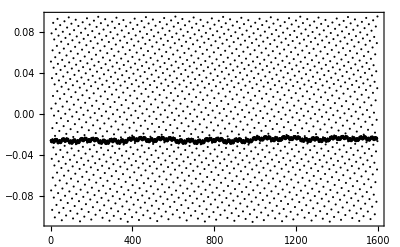

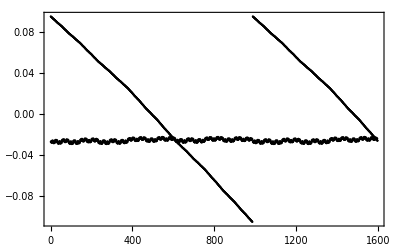

```mathematica
(* groundstate wavefunction *)
wf=vecs[[1]];
(* derivative *)
om=LogDerivative[wf];
ListPlot[{wf,om},PlotRange->All]
(* in perp space *)
wfp =Table[wf[[norm[l,j]]],{j,Length[wf]}];
omp=Table[om[[norm[l,j]]],{j,Length[wf]}];
ListPlot[{wfp,omp},PlotRange->All]
```

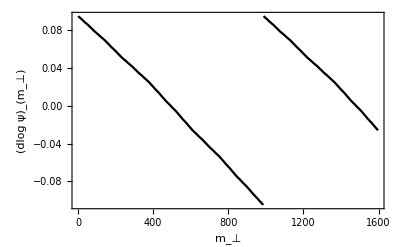

/home/nicolas/git/talks/Séminaire CALIN/img/state_spec_edge.pdf

```mathematica
ListPlot[omp,Joined->True,Frame->True,PlotStyle->Black,FrameLabel->stylize/@{"m_⊥","(dlog ψ)_(m_⊥)"}]
Export[NotebookDirectory[]<>"state_spec_edge.pdf",%]
```

```mathematica
(* potentials *)
Potentials[l_,C0_String,λ_]:=StringPartition[FiboSub[l,C0],1]/.{"A"->λ,"B"->-λ};
```

```mathematica
FiboPots=Potentials[l,"B",λ];
FiboHeights=Heights[FiboPots];
```

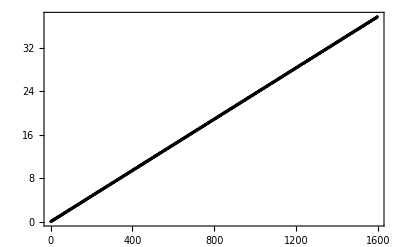

```mathematica
ListPlot[FiboHeights,PlotRange->All]
```

```mathematica
(* energy shift of the groundstate *)
δE=2.+vals[[1]];
(* a small corrective term accounting for higher order in λ *)
corr=1.013;
(* reduced potential (the perturbative expression of ω, see notes) *)
PertOm=FiboHeights-corr δE Range[Length[FiboHeights]];
(* in perp space *)
PertOmP=Table[PertOm[[norm[l,j]]],{j,Length[wf]}];
```

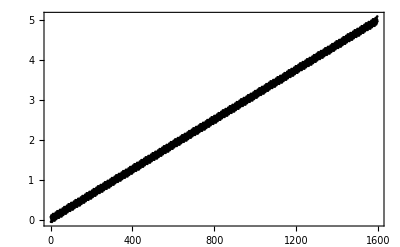

```mathematica
ListPlot[PertOm,PlotRange->All]
```

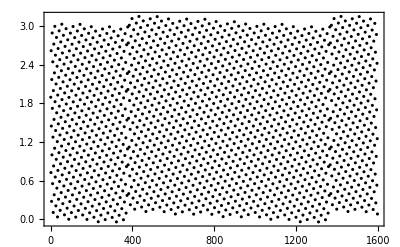

```mathematica
ListPlot[PertOmP,PlotRange->All]
```